# Project 7

## Question 2

Import the Data

```mathematica
A=ImageData[
Import["C:\\Users\\struther\\Desktop\\23-24-Classes\\Fall 2023 Courses\\SciComp\\peppers.png"]];
Image[A]
```

-Graphics-

## Code Bits

### CutOff: Input a vector of singular values and a scalar 0<p<1

Old fashioned loop.

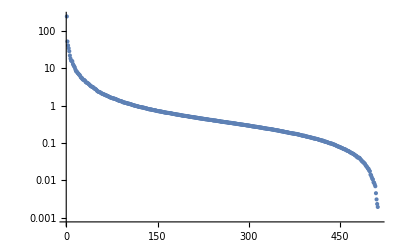

```mathematica
σ=SingularValueList[A];
ListLogPlot[σ,PlotRange->All]
```

```mathematica
σ=SingularValueList[A]; p=0.98;
energy=Accumulate[σ^2];energy=energy/energy⟦-1⟧;
k=1;
While[ energy⟦k⟧<p^2,k++]
{k,p^2,energy⟦1;;k⟧}
```

{7,0.9604,{0.859684,0.899142,0.923423,0.94054,0.952361,0.959361,0.964166}}

Computing an indicator.

```mathematica
σ=SingularValueList[A]; p=0.98;
energy=Accumulate[σ^2];energy=energy/energy⟦-1⟧;
k=FirstPosition[Sign[energy-p^2],1]⟦1⟧;
{k,p^2,energy⟦1;;k⟧}
```

{7,0.9604,{0.859684,0.899142,0.923423,0.94054,0.952361,0.959361,0.964166}}

There are lots of other ways to do the same thing.

```mathematica
CutOff[σ_,p_]:= Module[{energy=Accumulate[σ^2]},
energy=energy/energy⟦-1⟧;
FirstPosition[Sign[energy-p^2],1]⟦1⟧
]
```

Test the function.  This is a very minimal test!

```mathematica
σ=SingularValueList[A]; p=0.98;
CutOff[σ,p]
```

7

### SVDCompress: Input an array X, a block size b, and a scalar 0<p<1

I think the intention is that the inner blocks are square and of size b×b. The input array is probably not square. Our test problem is square! It is easy enough to count the sub pictures using modular arithmetic.   Here is a plot of the sub images demonstrating the required arithmetic.

```mathematica
{m,n}=Dimensions[A];
b=123;
{{q1,r1},{q2,r2}}=QuotientRemainder[{m,n},b];
MatrixPlot[A,ColorFunction->GrayLevel,Mesh->{b*Range[1,q1],b*Range[1,q2]}
]
```

-Graphics-

Here is a plot of the each of the sub images

```mathematica
GraphicsGrid[Table[
MatrixPlot[A⟦1+(i-1)*b;;i*b,1+(j-1)*b;;j*b⟧,ColorFunction->GrayLevel,Frame->False],
{i,1,q1},{j,1,q2}],
Spacings->{0,0}]
```

-Graphics-

So we know how to split up an image.  Lets see how to compress a single sub image.

```mathematica
b
```

123

```mathematica
{i,j}={2,3};
p=0.999;
AComp=A;
SubMat=AComp⟦1+(i-1)*b;;i*b,1+(j-1)*b;;j*b⟧;
{U,S,V}=SingularValueDecomposition[SubMat];
σ=Diagonal[S];
k=CutOff[σ,p]
B=U⟦All,1;;k⟧.S⟦1;;k,1;;k⟧.V⟦All,1;;k⟧ᵀ;
AComp⟦1+(i-1)*b;;i*b,1+(j-1)*b;;j*b⟧=B;
Image[AComp]
```

19

-Graphics-

The amount of data b×b sub image was originally b^2.  It has been reduced to k+2 b k bits of data: 
	k	k singular values σ_(1:k)
	k×b 	k right singular vectors of length b
	k×b 	k left singular vectors of length b.
We are supposed to keep track of how much data we need to store.  I made a function to do this to a sub image.

```mathematica
SubImageCompress[ASub_,p_]:= Module[{b,U,S,V,σ,k},
(* compression computation is correct only for square subimages *)
b=Length[ASub];
{U,S,V}=SingularValueDecomposition[ASub];
σ=Diagonal[S];
k=CutOff[σ,p];
(* return compressed sub image and potential reduced data *)
{U⟦All,1;;k⟧.S⟦1;;k,1;;k⟧.V⟦All,1;;k⟧ᵀ,k+2.0 b k}
]
```

Test the code.

```mathematica
p=0.99;
b=100;
{rng1,rng2}={10;;10+b,50;;50+b};
AComp=A;
ASub=AComp⟦rng1,rng2⟧;
{ASubComp,s}=SubImageCompress[ASub,p];
AComp⟦rng1,rng2⟧=ASubComp;
TabView[{"A"->Image[A],"AComp"->Image[AComp],"AComp-A"->MatrixPlot[AComp-A]},2]
```

123

Now all we really need to do is put everything together.  I need to loop through all of the sub images saving the data for the compressed image and adding up the space I need for the compressed image.

```mathematica
SVDCompress[A_,b_,p_]:=Module[{AComp=A,m,n,q1,r1,q2,r2,storage,s},
(* Input is a matrix A and a square block size b and quality factor 0<p<1 *)
(* Compute subblocks *)
{m,n}=Dimensions[AComp];
{{q1,r1},{q2,r2}}=QuotientRemainder[{m,n},b];
(* storage for unporcessed L shape is *)
storage=r1*n+r2*m-r1*r2;
(* Process each sub block *)
Do[
rng1=1+(i-1)*b;;i*b;
rng2=1+(j-1)*b;;j*b;
{AComp⟦rng1,rng2⟧, s}=SubImageCompress[AComp⟦rng1,rng2⟧,p];
(* Accumulate storage *)
storage+=s,
{i,1,q1},{j,1,q2}];
(* return compressed image and potential compression *)
{AComp,storage/(m n)}
]
```

Test the thing.

```mathematica
{b,p}={50,0.99};
{AComp,comp}=SVDCompress[A,b,p];
comp
TabView[{"A"->Image[A],"AComp"->Image[AComp],"AComp-A"->MatrixPlot[AComp-A]},2]
```

0.123768

123

We are supposed to mess around a bit with the block size b and 0<p<1.

```mathematica
{b,p}={8,0.9};
{AComp,comp}=SVDCompress[A,b,p];
comp
TabView[{"A"->Image[A],"AComp"->Image[AComp],"AComp-A"->MatrixPlot[AComp-A]},2]
```

0.26569

123

## Question 3

I do not have matlab on the laptop I am on. I am going to make some data that looks like the data in the picture.  The data looks like an S curve on a plane in 3D. Here is an S curve.

```mathematica
Clear[p,t]
p[t_]:={t(1-t)(2-t), 0.5 +0.01Sin[ t^3], t}
ParametricPlot3D[ p[t],{t, 0, 2},
PlotRange->{{-1,1},{0,1},{0,2}},
AxesLabel->{"x","y","z"}
]
```

-Graphics3D-

We need to get some data out of this thing.

```mathematica
SampleSize=123;
ϵ=0.1;
AASData=Table[
t=RandomReal[{0,2}];
p[t]+ ϵ RandomReal[{-1,1},3],
{SampleSize}];
Show[
ParametricPlot3D[ p[t],{t, 0, 2},
PlotRange->Automatic,
PlotStyle->Red,
AxesLabel->{"x","y","z"}
],
ListPointPlot3D[AASData],
PlotRange->All
]
```

-Graphics3D-

The data looks like this!

```mathematica
TabView[{"Pic"->MatrixPlot[AASDataᵀ],"Data"->MatrixForm[AASDataᵀ]}]
```

12

We want to try to recover the curve from the data!   This is what we are going to do in class! The first thing we need to do is  center the data on the origin.

```mathematica
middle=Map[Mean,AASDataᵀ];
AASDataCentered=(AASDataᵀ-middle)ᵀ;
TabView[{"Pic"->MatrixPlot[AASDataCenteredᵀ],"Data"->MatrixForm[AASDataCenteredᵀ]}]
```

12

```mathematica
SingularValueList[AASDataCentered]
{U,S,V}=SingularValueDecomposition[AASDataCentered,2];
MatrixForm[V]
```

{7.00703,1.60417,0.61381}

(-0.389452 | 0.920872
-0.00183162 | -0.0202713
0.921045 | 0.389338)

```mathematica
Data2D=(Vᵀ.AASDataCenteredᵀ)ᵀ;
Data3D=(V.Vᵀ.AASDataCenteredᵀ)ᵀ;
TabView[{
"Flat"->ListPointPlot3D[Data3D,AxesLabel->{"x","y","z"}],
"2D"->ListPlot[Data2D,AxesLabel->{"p_1","p_2"}]
}]
```

12

The command fit performs a linear least squares fit to the data.  I think the cubic fit looks good.   You should not fit a high degree polynomial to data.

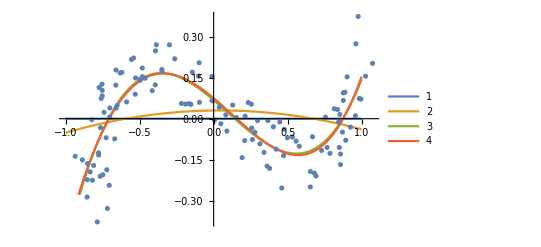

```mathematica
p2[x_]=Fit[Data2D,{1,x,x^2},x];
p3[x_]=Fit[Data2D,{1,x,x^2,x^3},x];
p4[x_]=Fit[Data2D,Table[x^i,{i,0,4}],x];
Show[
Plot[ {p1[x],p2[x],p3[x],p4[x]},{x, -1, 1},PlotLegends->Automatic],
ListPlot[Data2D,
AxesLabel->{"x","y"}
],
PlotRange->All
]
```

In a cubic
	a_0+a_1 x +a_2 x^2+a_3 x^3
there are 4 unknowns. The cubic is specified by the 4 coefficients.  The x is just a dummy variable.   The Least Squares fit for the cubic is the minimizer of
	||X.a-y||
where 
	{1,x_1,x_1^2,x_1^3}.{a_0,a_1,a_2,a_3}-y_1≈0
	{1,x_2,x_2^2,x_2^3}.{a_0,a_1,a_2,a_3}-y_2≈0
	…
so the ith row of the matrix X is 
	X_(i,All)=(1,x_i,x_i^2,x_i^3)
From any linear algebra text the minimizer is given by 
	(XᵀX)^-1 Xᵀy
or equivalently if X=Q R by 
	R^-1 Qᵀy
Of course, it is not efficient to explicitly form the Inverse.  Instead you just use linear solve.

```mathematica
X=Table[
x=Data2D⟦i,1⟧;
{1,x,x^2,x^3},
{i, 1, Length[Data2D]}];
y=Table[
y=Data2D⟦i,2⟧;
y,
{i, 1, Length[Data2D]}];
(* Normal Equations *)
Inverse[Xᵀ.X].Xᵀ.y
LinearSolve[Xᵀ.X,Xᵀ.y]
(* QR Equations *)
{Q,R}=QRDecomposition[X];Q=Qᵀ;
Inverse[R].Qᵀ.y
LinearSolve[R,Qᵀ.y]
```

{0.0676476,-0.458275,-0.233142,0.767738}

{0.0676476,-0.458275,-0.233142,0.767738}

{0.0676476,-0.458275,-0.233142,0.767738}

«1 more identical outputs»

Of course, the coefficients match the result from the built in Fit command.

```mathematica
Clear[x]
p3[x]
```

0.0676476-0.458275 x-0.233142 x^2+0.767738 x^3

We are now in a position to recreate our curve in ℝ^3

```mathematica
TabView[{
"2D"->ParametricPlot[{s,p3[s]},{s,-1,1}],
"3D"->ParametricPlot3D[V.{s,p3[s]},{s,-1,1},PlotStyle->Green],
"3D+Data"->Show[
ParametricPlot3D[V.{s,p3[s]}+middle,{s,-1,1},PlotStyle->Green],
ListPointPlot3D[AASData],
PlotRange->All
]
}]
```

123

```mathematica
ParametricPlot3D[Vᵀ.{s,p3[s]},{s,-1,1}]
```

Dot::dotsh: Tensors {{-0.389452,-0.00183162,0.921045},{0.920872,-0.0202713,0.389338}} and {-0.999959,-0.474863} have incompatible shapes.

Dot::dotsh: Tensors {{-0.389452,-0.00183162,0.921045},{0.920872,-0.0202713,0.389338}} and {-0.959143,-0.384709} have incompatible shapes.

Dot::dotsh: Tensors {{-0.389452,-0.00183162,0.921045},{0.920872,-0.0202713,0.389338}} and {-0.918326,-0.302693} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics3D-